# FUNCIÓN PARA DISTRIBUCIONES

```mathematica
Clear[plotDistribution];

Options[plotDistribution] = {
   "PlotLabel" -> "Distribución de datos",
   "PlotColor" -> Blue,
   "Bins" -> Automatic,
   "BootstrapReps" -> 100,
   "Discrete" -> False   (* True: datos discretos (por defecto bins de ancho 1); False: continuos *)
};

plotDistribution[data_List, opts : OptionsPattern[]] := Module[{
    dataPos, mean, var, skew, kurt,
    dists, names, kParams, fits, logs, aics, best, bestFit,
    findDist, findDistLogL, findDistAIC, findDistParams,
    hist, binEdges, binWidth, xmin, xmax, curve,
    ksPower, alphaCI,
    plotTitle, plotColor, binSpec, bootstrapReps, discreteQ
  },

  (* Opciones *)
  {plotTitle, plotColor, binSpec, bootstrapReps, discreteQ} = 
    OptionValue[{"PlotLabel", "PlotColor", "Bins", "BootstrapReps", "Discrete"}];

  (* Eliminar ceros o negativos *)
  dataPos = Select[data, # > 0 &];
  If[Length[dataPos] == 0, Return["No hay datos positivos para analizar."]];

  (* Estadísticos descriptivos *)
  mean = Mean[dataPos];
  var = Variance[dataPos];
  skew = Skewness[dataPos];
  kurt = Kurtosis[dataPos];

  (* Distribuciones candidatas *)
  dists = {
    ParetoDistribution[a, b],
    ExponentialDistribution[λ],
    LogNormalDistribution[μ, σ],
    GammaDistribution[α, β],
    WeibullDistribution[α, β]
  };
  names = {"Power law", "Exponential", "Lognormal", "Gamma", "Stretched exponential"};
  kParams = {2, 1, 2, 2, 2};

  (* Ajustes *)
  fits = Quiet[Check[EstimatedDistribution[dataPos, #], $Failed]] & /@ dists;
  logs = MapThread[If[#2 =!= $Failed, LogLikelihood[#2, dataPos], -Infinity] &, {dists, fits}];
  aics = -2 logs + 2 kParams;

  (* Mejor modelo de las candidatas *)
  best = Ordering[aics, 1][[1]];
  bestFit = fits[[best]];

  (* FindDistribution *)
  findDist = Quiet[
    If[discreteQ,
      Check[FindDistribution[dataPos, TargetFunctions -> "Discrete"], $Failed],
      Check[FindDistribution[dataPos], $Failed]
    ]
  ];
  If[findDist =!= $Failed,
    findDistParams = Length[findDist];
    findDistLogL = LogLikelihood[findDist, dataPos];
    findDistAIC = -2 findDistLogL + 2 findDistParams;
    ,
    findDist = "No disponible";
    findDistLogL = "N/A";
    findDistAIC = "N/A";
  ];

  (* Análisis de ley de potencia *)
  If[Head[fits[[1]]] === ParetoDistribution && fits[[1]] =!= $Failed,
    ksPower = KolmogorovSmirnovTest[dataPos, fits[[1]], "PValue"];
    alphaCI = Module[{alphaBoot},
      alphaBoot = Table[
        samp = RandomChoice[dataPos, Length[dataPos]];
        fit = Quiet[Check[EstimatedDistribution[samp, ParetoDistribution[a, b]], $Failed]];
        If[fit =!= $Failed, fit[[2]], Nothing] /. ParetoDistribution[_, a_] :> a,
        {bootstrapReps}
      ];
      If[Length[alphaBoot] > 1, Quantile[alphaBoot, {0.025, 0.975}], {None, None}]
    ];
    ,
    ksPower = "N/A";
    alphaCI = {None, None}
  ];

  (* --- GRÁFICO --- *)
  (* Determinar especificación de bins: si discreto y el usuario no especificó, usar ancho 1; de lo contrario, lo que el usuario haya puesto *)
  binSpecFinal = If[discreteQ && binSpec === Automatic, {1}, binSpec];

  hist = Histogram[dataPos,
    binSpecFinal,
    "Probability",
    ChartStyle -> plotColor,
    Frame -> True,
    FrameLabel -> {"x", "P(x)"},
    PlotLabel -> plotTitle,
    LabelStyle -> Directive[14]
  ];

  binEdges = HistogramList[dataPos, binSpecFinal][[1]];
  binWidth = Mean[Differences[binEdges]];

  xmin = Min[dataPos] - 0.1*(Max[dataPos] - Min[dataPos]);
  xmax = Max[dataPos] + 0.1*(Max[dataPos] - Min[dataPos]);

  curve = If[discreteQ,
    ListPlot[
      Table[{k, PDF[bestFit, k]}, {k, Round[xmin], Round[xmax]}],
      PlotStyle -> {Black, Thick, Dashed},
      Joined -> True
    ],
    Plot[
      PDF[bestFit, x] * binWidth,
      {x, xmin, xmax},
      PlotStyle -> {Black, Thick, Dashed},
      PlotRange -> All
    ]
  ];

  (* Impresión de resultados *)
  Print[Style["Estadísticos descriptivos:", Bold, 14]];
  Print[Style["  Media     = " <> ToString[NumberForm[N[mean], {Infinity, 4}]], 14]];
  Print[Style["  Varianza  = " <> ToString[NumberForm[N[var], {Infinity, 4}]], 14]];
  Print[Style["  Asimetría = " <> ToString[NumberForm[N[skew], {Infinity, 4}]], 14]];
  Print[Style["  Curtosis  = " <> ToString[NumberForm[N[kurt], {Infinity, 4}]], 14]];
  Print[""];

  Print[Style["Ajuste de distribuciones (candidatas):", Bold, 14]];
  Print[Style[TableForm[Transpose[{
      names,
      fits,
      NumberForm[N[#], {Infinity, 4}] & /@ logs,
      NumberForm[N[#], {Infinity, 4}] & /@ aics
    }], TableHeadings -> {None, {"Distribución", "Ajuste", "LogL", "AIC"}}], 14]];
  Print[""];

  Print[Style["Distribución sugerida por FindDistribution:", Bold, 14]];
  Print[Style["  Modelo = " <> ToString[findDist], 14]];
  Print[Style["  LogL   = " <> ToString[If[findDistLogL =!= "N/A", NumberForm[N[findDistLogL], {Infinity, 4}], "N/A"]], 14]];
  Print[Style["  AIC    = " <> ToString[If[findDistAIC =!= "N/A", NumberForm[N[findDistAIC], {Infinity, 4}], "N/A"]], 14]];
  Print[""];

  Print[Style["Mejor modelo (menor AIC entre candidatas): " <> names[[best]] <> 
    ", AIC = " <> ToString[NumberForm[N[aics[[best]]], {Infinity, 4}]], Bold, 14]];
  Print[""];

  If[Head[fits[[1]]] === ParetoDistribution && fits[[1]] =!= $Failed,
    Print[Style["Detalles de la ley de potencia (Pareto):", Bold, 14]];
    Print[Style["  α (exponente) = " <> ToString[NumberForm[N[fits[[1, 2]]], {Infinity, 4}]], 14]];
    Print[Style["  xmin (umbral) = " <> ToString[NumberForm[N[fits[[1, 1]]], {Infinity, 4}]], 14]];
    Print[Style["  p-valor KS    = " <> ToString[NumberForm[N[ksPower], {Infinity, 4}]], 14]];
    If[NumericQ[ksPower] && ksPower > 0.05,
      Print[Style["    → No se rechaza que los datos sigan una ley de potencia.", 14]],
      If[NumericQ[ksPower], Print[Style["    → Se rechaza la ley de potencia (p < 0.05).", 14]]]
    ];
    Print[Style["  IC 95% bootstrap para α = [" <> 
      ToString[NumberForm[N[alphaCI[[1]]], {Infinity, 4}]] <> ", " <> 
      ToString[NumberForm[N[alphaCI[[2]]], {Infinity, 4}]] <> "]", 14]];
  ];

  Show[hist, curve, PlotRange -> All, LabelStyle -> Directive[14]]
];
```

# BOLIVAR

```mathematica
NIÑOBOLIVAR = {17,9,6,5,5,9,2,2,4,2,5,6,2,1,6,4,8,6,7,18};

NIÑOPESADOBOLIVAR = {94,27,8,8,6,21,2,2,5,2,15,12,2,2,17,8,10,10,26,117};

BOLIVAR = {17, 16, 6, 10, 2, 12, 16, 7, 4, 10, 2, 13, 5, 2, 9, 0, 9, 14, 8, 9, 15, 7, 12, 19};

BOLIVARPESADO = {45, 24, 8, 17, 4, 16, 37, 10, 4, 14, 2, 22, 6, 2, 12, 0, 10, 25, 12, 14, 25, 10, 25, 50};

INTERBOLIVAR = {13, 7, 4, 3, 0, 5, 9, 1, 1, 3, 0, 3, 3, 0, 1, 0, 1, 4, 4, 0, 7, 3, 5, 15};

INTERBOLIVARPESADO = {866.50246305, 470.23809524, 600., 350., 0., 600., 1525., 200., 
      100., 450., 0., 170., 316.66666667, 0., 100., 0., 100., 
      653.33333333, 425., 0., 1200., 266.66666667, 732.22222222, 982.93103448};
```

KolmogorovSmirnovTest::ties: Ties exist in the data and will be ignored for the KolmogorovSmirnov test, which assumes unique values.

Estadísticos descriptivos:

Media     = 6.2000

Varianza  = 20.3789

Asimetría = 1.4613

Curtosis  = 4.6898

Ajuste de distribuciones (candidatas):

Distribución | Ajuste | LogL | AIC
Power law | ParetoDistribution[1.,0.631235] | -60.8855 | 125.7709
Exponential | ExponentialDistribution[0.16129] | -56.4910 | 114.9820
Lognormal | LogNormalDistribution[1.5842,0.718748] | -53.4578 | 110.9156
Gamma | GammaDistribution[2.23269,2.77692] | -53.5051 | 111.0101
Stretched exponential | WeibullDistribution[1.51735,6.9213] | -53.9784 | 111.9569

Distribución sugerida por FindDistribution:

Modelo = PoissonDistribution[4.81818]

LogL   = -65.8286

AIC    = 133.6571

Mejor modelo (menor AIC entre candidatas): Lognormal, AIC = 110.9156

Detalles de la ley de potencia (Pareto):

α (exponente) = 0.6312

xmin (umbral) = 1.0000

p-valor KS    = 0.0176

→ Se rechaza la ley de potencia (p < 0.05).

IC 95% bootstrap para α = [0.5596, 1.3874]

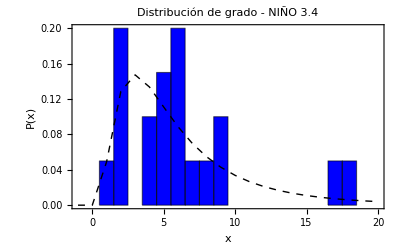

KolmogorovSmirnovTest::ties: Ties exist in the data and will be ignored for the KolmogorovSmirnov test, which assumes unique values.

Estadísticos descriptivos:

Media     = 19.7000

Varianza  = 933.6947

Asimetría = 2.4440

Curtosis  = 7.6743

Ajuste de distribuciones (candidatas):

Distribución | Ajuste | LogL | AIC
Power law | ParetoDistribution[2.,0.649824] | -73.2616 | 150.5232
Exponential | ExponentialDistribution[0.0507614] | -79.6124 | 161.2247
Lognormal | LogNormalDistribution[2.23203,1.17776] | -76.2915 | 156.5831
Gamma | GammaDistribution[0.793645,24.8222] | -79.2291 | 162.4581
Stretched exponential | WeibullDistribution[0.814293,17.1513] | -78.6843 | 161.3687

Distribución sugerida por FindDistribution:

Modelo = No disponible

LogL   = N/A

AIC    = N/A

Mejor modelo (menor AIC entre candidatas): Power law, AIC = 150.5232

Detalles de la ley de potencia (Pareto):

α (exponente) = 0.6498

xmin (umbral) = 2.0000

p-valor KS    = 0.1376

→ No se rechaza que los datos sigan una ley de potencia.

IC 95% bootstrap para α = [0.4890, 0.9524]

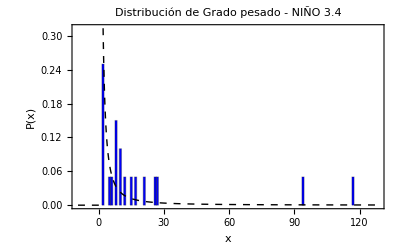

KolmogorovSmirnovTest::ties: Ties exist in the data and will be ignored for the KolmogorovSmirnov test, which assumes unique values.

Estadísticos descriptivos:

Media     = 9.7391

Varianza  = 25.1107

Asimetría = 0.0601

Curtosis  = 2.0452

Ajuste de distribuciones (candidatas):

Distribución | Ajuste | LogL | AIC
Power law | ParetoDistribution[2.,0.712133] | -79.0480 | 162.0961
Exponential | ExponentialDistribution[0.102679] | -75.3515 | 152.7030
Lognormal | LogNormalDistribution[2.09738,0.668195] | -71.6023 | 147.2046
Gamma | GammaDistribution[2.95299,3.29805] | -69.7115 | 143.4231
Stretched exponential | WeibullDistribution[2.07345,10.975] | -68.6909 | 141.3817

Distribución sugerida por FindDistribution:

Modelo = DiscreteUniformDistribution[{2, 16}]

LogL   = -Infinity

AIC    = Infinity

Mejor modelo (menor AIC entre candidatas): Stretched exponential, AIC = 141.3817

Detalles de la ley de potencia (Pareto):

α (exponente) = 0.7121

xmin (umbral) = 2.0000

p-valor KS    = 0.0101

→ Se rechaza la ley de potencia (p < 0.05).

IC 95% bootstrap para α = [0.6136, 1.1074]

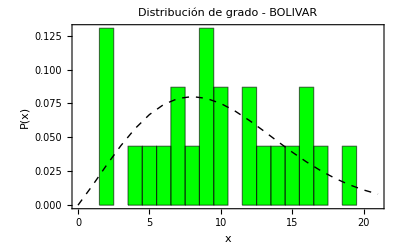

KolmogorovSmirnovTest::ties: Ties exist in the data and will be ignored for the KolmogorovSmirnov test, which assumes unique values.

Estadísticos descriptivos:

Media     = 17.1304

Varianza  = 170.2095

Asimetría = 1.0860

Curtosis  = 3.5046

Ajuste de distribuciones (candidatas):

Distribución | Ajuste | LogL | AIC
Power law | ParetoDistribution[2.,0.54626] | -94.9541 | 193.9082
Exponential | ExponentialDistribution[0.0583756] | -88.3397 | 178.6794
Lognormal | LogNormalDistribution[2.52378,0.867573] | -87.4152 | 178.8304
Gamma | GammaDistribution[1.72478,9.93195] | -86.5921 | 177.1842
Stretched exponential | WeibullDistribution[1.37886,18.7961] | -86.6566 | 177.3132

Distribución sugerida por FindDistribution:

Modelo = No disponible

LogL   = N/A

AIC    = N/A

Mejor modelo (menor AIC entre candidatas): Gamma, AIC = 177.1842

Detalles de la ley de potencia (Pareto):

α (exponente) = 0.5463

xmin (umbral) = 2.0000

p-valor KS    = 0.0119

→ Se rechaza la ley de potencia (p < 0.05).

IC 95% bootstrap para α = [0.4700, 0.8925]

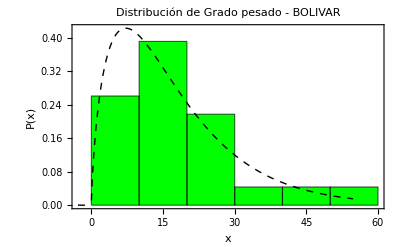

KolmogorovSmirnovTest::ties: Ties exist in the data and will be ignored for the KolmogorovSmirnov test, which assumes unique values.

Estadísticos descriptivos:

Media     = 4.8421

Varianza  = 15.2515

Asimetría = 1.3638

Curtosis  = 4.1216

Ajuste de distribuciones (candidatas):

Distribución | Ajuste | LogL | AIC
Power law | ParetoDistribution[1.,0.784059] | -47.8550 | 99.7100
Exponential | ExponentialDistribution[0.206522] | -48.9696 | 99.9393
Lognormal | LogNormalDistribution[1.27541,0.807441] | -47.1289 | 98.2578
Gamma | GammaDistribution[1.80475,2.68298] | -47.3061 | 98.6123
Stretched exponential | WeibullDistribution[1.3607,5.31979] | -47.6193 | 99.2386

Distribución sugerida por FindDistribution:

Modelo = PoissonDistribution[3.38095]

LogL   = -60.5391

AIC    = 123.0783

Mejor modelo (menor AIC entre candidatas): Lognormal, AIC = 98.2578

Detalles de la ley de potencia (Pareto):

α (exponente) = 0.7841

xmin (umbral) = 1.0000

p-valor KS    = 0.0084

→ Se rechaza la ley de potencia (p < 0.05).

IC 95% bootstrap para α = [0.6210, 1.2295]

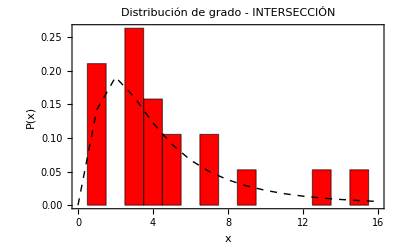

KolmogorovSmirnovTest::ties: Ties exist in the data and will be ignored for the KolmogorovSmirnov test, which assumes unique values.

Estadísticos descriptivos:

Media     = 532.0295

Varianza  = 154699.1195

Asimetría = 0.9887

Curtosis  = 3.3551

Ajuste de distribuciones (candidatas):

Distribución | Ajuste | LogL | AIC
Power law | ParetoDistribution[100.,0.724787] | -138.8285 | 281.6571
Exponential | ExponentialDistribution[0.0018796] | -138.2573 | 278.5146
Lognormal | LogNormalDistribution[5.98489,0.814237] | -136.7681 | 277.5362
Gamma | GammaDistribution[1.86279,285.608] | -136.4335 | 276.8669
Stretched exponential | WeibullDistribution[1.43581,588.01] | -136.5300 | 277.0600

Distribución sugerida por FindDistribution:

Modelo = WeibullDistribution[0.440253, 300.602, 99.9434]

LogL   = -130.8848

AIC    = 267.7696

Mejor modelo (menor AIC entre candidatas): Gamma, AIC = 276.8669

Detalles de la ley de potencia (Pareto):

α (exponente) = 0.7248

xmin (umbral) = 100.0000

p-valor KS    = 0.1546

→ No se rechaza que los datos sigan una ley de potencia.

IC 95% bootstrap para α = [0.5765, 1.0537]

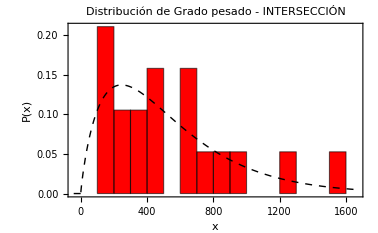

```mathematica
plotDistribution[NIÑOBOLIVAR,"PlotLabel"->"Distribución de grado - NIÑO 3.4","PlotColor"->Blue,"Discrete"->True,"BootstrapReps"->500,"Bins"->50]

plotDistribution[NIÑOPESADOBOLIVAR,"PlotLabel"->"Distribución de Grado pesado - NIÑO 3.4","PlotColor"->Blue,"Discrete"->False,"BootstrapReps"->500,"Bins"->80]

plotDistribution[BOLIVAR,"PlotLabel"->"Distribución de grado - BOLIVAR","PlotColor"->Green,"Discrete"->True,"BootstrapReps"->500,"Bins"->100]

plotDistribution[BOLIVARPESADO,"PlotLabel"->"Distribución de Grado pesado - BOLIVAR","PlotColor"->Green,"Discrete"->False,"BootstrapReps"->500,"Bins"->7]

plotDistribution[INTERBOLIVAR,"PlotLabel"->"Distribución de grado - INTERSECCIÓN","PlotColor"->Red,"Discrete"->True,"BootstrapReps"->500,"Bins"->50]

plotDistribution[INTERBOLIVARPESADO,"PlotLabel"->"Distribución de Grado pesado - INTERSECCIÓN","PlotColor"->Red,"Discrete"->False,"BootstrapReps"->500,"Bins"->15]
```

# CALAMAR

```mathematica
NIÑOCALAMAR = {24, 23, 12, 17, 8, 16, 20, 10, 12, 11, 7, 15, 14, 9, 14, 10, 8, 21, 13, 6, 17, 15, 21, 25};

NIÑOPESADOCALAMAR = {292, 99, 39, 48, 10, 34, 91, 18, 18, 32, 8, 52, 57, 12, 34, 16, 16, 105, 32, 6, 46, 52, 113, 364};

CALAMAR = {23, 20, 15, 20, 10, 24, 25, 16, 15, 16, 15, 19, 20, 4, 17, 8, 14, 20, 15, 9, 20, 16, 21, 24};

CALAMARPESADO = {236, 100, 36, 73, 20, 54, 119, 38, 28, 44, 20, 60, 68, 6, 46, 16, 30, 101, 30, 26, 69, 47, 101, 226};

INTERCALAMAR = {22, 19, 10, 14, 5, 15, 20, 7, 7, 9, 7, 14, 13, 2, 11, 6, 5, 17, 8, 4, 16, 10, 19, 24};

INTERCALAMARPESADO = {2985.90970798, 2899.91854637, 1100., 2015.71428571, 1033.33333333,
       2040., 3033.33333333, 1071.42857143, 850., 1131.66666667,
       850., 1617.57575758, 1629.70588235, 200., 1775.,
       666.66666667, 483.33333333, 2337.7134647, 852.77777778,
       1100., 2411.66666667, 1418.33333333, 2741.53679654, 2549.76693002};
```

KolmogorovSmirnovTest::ties: Ties exist in the data and will be ignored for the KolmogorovSmirnov test, which assumes unique values.

Estadísticos descriptivos:

Media     = 14.5000

Varianza  = 31.0435

Asimetría = 0.3513

Curtosis  = 2.0720

Ajuste de distribuciones (candidatas):

Distribución | Ajuste | LogL | AIC
Power law | ParetoDistribution[6.,1.2384] | -81.2503 | 166.5006
Exponential | ExponentialDistribution[0.0689655] | -88.1796 | 178.3591
Lognormal | LogNormalDistribution[2.59925,0.395359] | -74.1655 | 152.3310
Gamma | GammaDistribution[6.83819,2.12044] | -73.9504 | 151.9008
Stretched exponential | WeibullDistribution[2.90829,16.3087] | -74.1932 | 152.3864

Distribución sugerida por FindDistribution:

Modelo = DiscreteUniformDistribution[{6, 22}]

LogL   = -Infinity

AIC    = Infinity

Mejor modelo (menor AIC entre candidatas): Gamma, AIC = 151.9008

Detalles de la ley de potencia (Pareto):

α (exponente) = 1.2384

xmin (umbral) = 6.0000

p-valor KS    = 0.0633

→ No se rechaza que los datos sigan una ley de potencia.

IC 95% bootstrap para α = [1.0818, 1.9901]

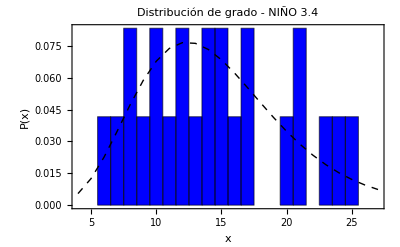

KolmogorovSmirnovTest::ties: Ties exist in the data and will be ignored for the KolmogorovSmirnov test, which assumes unique values.

Estadísticos descriptivos:

Media     = 66.4167

Varianza  = 7575.2101

Asimetría = 2.4658

Curtosis  = 8.3124

Ajuste de distribuciones (candidatas):

Distribución | Ajuste | LogL | AIC
Power law | ParetoDistribution[6.,0.541312] | -126.0692 | 256.1385
Exponential | ExponentialDistribution[0.0150565] | -124.7028 | 251.4055
Lognormal | LogNormalDistribution[3.63912,1.02591] | -122.0073 | 248.0146
Gamma | GammaDistribution[1.03275,64.3107] | -124.6948 | 253.3897
Stretched exponential | WeibullDistribution[0.946668,64.4722] | -124.6303 | 253.2606

Distribución sugerida por FindDistribution:

Modelo = No disponible

LogL   = N/A

AIC    = N/A

Mejor modelo (menor AIC entre candidatas): Lognormal, AIC = 248.0146

Detalles de la ley de potencia (Pareto):

α (exponente) = 0.5413

xmin (umbral) = 6.0000

p-valor KS    = 0.0599

→ No se rechaza que los datos sigan una ley de potencia.

IC 95% bootstrap para α = [0.4671, 0.8522]

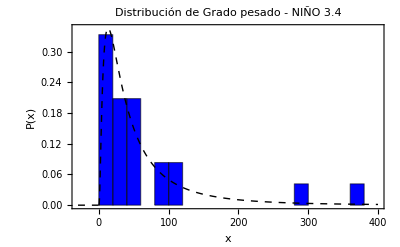

KolmogorovSmirnovTest::ties: Ties exist in the data and will be ignored for the KolmogorovSmirnov test, which assumes unique values.

Estadísticos descriptivos:

Media     = 16.9167

Varianza  = 28.4275

Asimetría = -0.6032

Curtosis  = 2.9151

Ajuste de distribuciones (candidatas):

Distribución | Ajuste | LogL | AIC
Power law | ParetoDistribution[4.,0.727387] | -97.9050 | 199.8100
Exponential | ExponentialDistribution[0.0591133] | -91.8792 | 185.7584
Lognormal | LogNormalDistribution[2.76108,0.408316] | -78.8233 | 161.6465
Gamma | GammaDistribution[7.60099,2.22559] | -76.5067 | 157.0134
Stretched exponential | WeibullDistribution[3.79937,18.7118] | -73.5558 | 151.1115

Distribución sugerida por FindDistribution:

Modelo = PoissonDistribution[10.8846]

LogL   = -111.5422

AIC    = 225.0845

Mejor modelo (menor AIC entre candidatas): Stretched exponential, AIC = 151.1115

Detalles de la ley de potencia (Pareto):

α (exponente) = 0.7274

xmin (umbral) = 4.0000

p-valor KS    = 0.0001

→ Se rechaza la ley de potencia (p < 0.05).

IC 95% bootstrap para α = [0.6789, 1.8329]

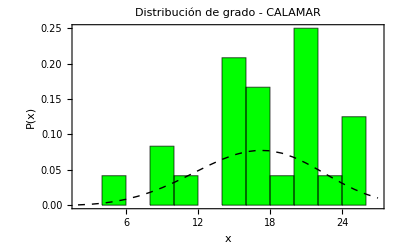

KolmogorovSmirnovTest::ties: Ties exist in the data and will be ignored for the KolmogorovSmirnov test, which assumes unique values.

Estadísticos descriptivos:

Media     = 66.4167

Varianza  = 3480.4275

Asimetría = 1.8081

Curtosis  = 5.7188

Ajuste de distribuciones (candidatas):

Distribución | Ajuste | LogL | AIC
Power law | ParetoDistribution[6.,0.480416] | -134.5533 | 273.1067
Exponential | ExponentialDistribution[0.0150565] | -124.7028 | 251.4055
Lognormal | LogNormalDistribution[3.87329,0.822051] | -122.3106 | 248.6211
Gamma | GammaDistribution[1.69717,39.1337] | -122.9744 | 249.9488
Stretched exponential | WeibullDistribution[1.27779,72.2056] | -123.5336 | 251.0672

Distribución sugerida por FindDistribution:

Modelo = No disponible

LogL   = N/A

AIC    = N/A

Mejor modelo (menor AIC entre candidatas): Lognormal, AIC = 248.6211

Detalles de la ley de potencia (Pareto):

α (exponente) = 0.4804

xmin (umbral) = 6.0000

p-valor KS    = 0.0032

→ Se rechaza la ley de potencia (p < 0.05).

IC 95% bootstrap para α = [0.4342, 1.1509]

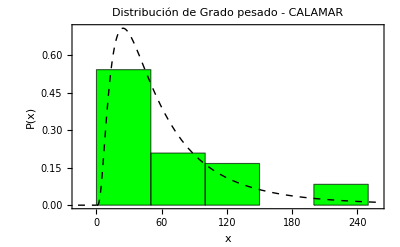

KolmogorovSmirnovTest::ties: Ties exist in the data and will be ignored for the KolmogorovSmirnov test, which assumes unique values.

Estadísticos descriptivos:

Media     = 11.8333

Varianza  = 37.8841

Asimetría = 0.3234

Curtosis  = 2.0249

Ajuste de distribuciones (candidatas):

Distribución | Ajuste | LogL | AIC
Power law | ParetoDistribution[2.,0.617242] | -91.0980 | 186.1960
Exponential | ExponentialDistribution[0.084507] | -83.3021 | 168.6042
Lognormal | LogNormalDistribution[2.31326,0.603989] | -77.4719 | 158.9438
Gamma | GammaDistribution[3.32872,3.55492] | -76.3363 | 156.6727
Stretched exponential | WeibullDistribution[2.08344,13.3867] | -75.9526 | 155.9052

Distribución sugerida por FindDistribution:

Modelo = DiscreteUniformDistribution[{2, 19}]

LogL   = -Infinity

AIC    = Infinity

Mejor modelo (menor AIC entre candidatas): Stretched exponential, AIC = 155.9052

Detalles de la ley de potencia (Pareto):

α (exponente) = 0.6172

xmin (umbral) = 2.0000

p-valor KS    = 0.0041

→ Se rechaza la ley de potencia (p < 0.05).

IC 95% bootstrap para α = [0.5662, 1.4703]

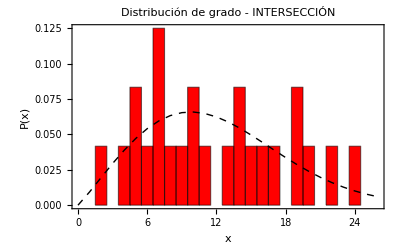

KolmogorovSmirnovTest::ties: Ties exist in the data and will be ignored for the KolmogorovSmirnov test, which assumes unique values.

Estadísticos descriptivos:

Media     = 1616.4742

Varianza  = 720831.3603

Asimetría = 0.2560

Curtosis  = 1.8573

Ajuste de distribuciones (candidatas):

Distribución | Ajuste | LogL | AIC
Power law | ParetoDistribution[200.,0.521001] | -212.8728 | 429.7457
Exponential | ExponentialDistribution[0.00061863] | -201.3121 | 404.6241
Lognormal | LogNormalDistribution[7.2177,0.644428] | -196.7339 | 397.4677
Gamma | GammaDistribution[3.09257,522.695] | -195.0160 | 394.0320
Stretched exponential | WeibullDistribution[2.04246,1825.18] | -194.3856 | 392.7711

Distribución sugerida por FindDistribution:

Modelo = UniformDistribution[{200.077, 3033.34}]

LogL   = -Infinity

AIC    = Infinity

Mejor modelo (menor AIC entre candidatas): Stretched exponential, AIC = 392.7711

Detalles de la ley de potencia (Pareto):

α (exponente) = 0.5210

xmin (umbral) = 200.0000

p-valor KS    = 0.0005

→ Se rechaza la ley de potencia (p < 0.05).

IC 95% bootstrap para α = [0.4841, 1.5569]

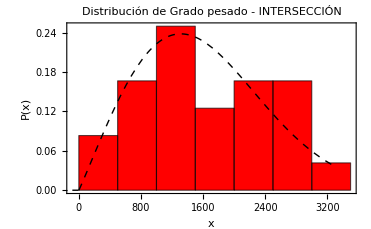

```mathematica
plotDistribution[NIÑOCALAMAR,"PlotLabel"->"Distribución de grado - NIÑO 3.4","PlotColor"->Blue,"Discrete"->True,"BootstrapReps"->500,"Bins"->200]

plotDistribution[NIÑOPESADOCALAMAR,"PlotLabel"->"Distribución de Grado pesado - NIÑO 3.4","PlotColor"->Blue,"Discrete"->False,"BootstrapReps"->500,"Bins"->20]

plotDistribution[CALAMAR,"PlotLabel"->"Distribución de grado - CALAMAR","PlotColor"->Green,"Discrete"->True,"BootstrapReps"->500,"Bins"->10]

plotDistribution[CALAMARPESADO,"PlotLabel"->"Distribución de Grado pesado - CALAMAR","PlotColor"->Green,"Discrete"->False,"BootstrapReps"->500,"Bins"->7]

plotDistribution[INTERCALAMAR,"PlotLabel"->"Distribución de grado - INTERSECCIÓN","PlotColor"->Red,"Discrete"->True,"BootstrapReps"->500,"Bins"->50]

plotDistribution[INTERCALAMARPESADO,"PlotLabel"->"Distribución de Grado pesado - INTERSECCIÓN","PlotColor"->Red,"Discrete"->False,"BootstrapReps"->500,"Bins"->8]
```

# TIMBUES

```mathematica
NIÑOTIMBUES = {24, 23, 12, 17, 8, 16, 20, 10, 12, 11, 7, 15, 14, 9, 14, 10, 8, 21, 13, 6, 17, 15, 21, 25};

NIÑOPESADOTIMBUES = {304, 104, 40, 48, 10, 36, 95, 18, 18, 33, 8, 54, 57, 12, 35, 16, 16, 111,
       34, 6, 48, 56, 119, 378};

TIMBUES = {23, 22, 14, 15, 9, 16, 21, 8, 12, 16, 3, 21, 19, 6, 14, 10, 9, 19, 15, 7, 18, 8, 21, 24};

TIMBUESPESADO = {269, 126, 26, 73, 14, 40, 120, 12, 20, 52, 4, 76, 84, 8, 38, 14, 12, 117,
       48, 10, 70, 14, 126, 283};

INTERTIMBUES = {22, 21, 10, 13, 5, 13, 18, 4, 7, 7, 2, 14, 12, 3, 10, 4, 4, 16, 10, 3, 14, 7, 19, 24};

INTERTIMBUESPESADO = {2322.38826489, 3883.2034632, 686.11111111, 2426.19047619, 733.33333333,
       1718.33333333, 3463.77289377, 514.28571429, 850., 1200.,
       200., 2490.90909091, 2593.1372549, 333.33333333, 1286.42857143,
       533.33333333, 350., 2317.5659824, 1715., 600.,
       3011.66666667, 356.94444444, 2672.70833333, 2071.56500451};
```

KolmogorovSmirnovTest::ties: Ties exist in the data and will be ignored for the KolmogorovSmirnov test, which assumes unique values.

Estadísticos descriptivos:

Media     = 14.5000

Varianza  = 31.0435

Asimetría = 0.3513

Curtosis  = 2.0720

Ajuste de distribuciones (candidatas):

Distribución | Ajuste | LogL | AIC
Power law | ParetoDistribution[6.,1.2384] | -81.2503 | 166.5006
Exponential | ExponentialDistribution[0.0689655] | -88.1796 | 178.3591
Lognormal | LogNormalDistribution[2.59925,0.395359] | -74.1655 | 152.3310
Gamma | GammaDistribution[6.83819,2.12044] | -73.9504 | 151.9008
Stretched exponential | WeibullDistribution[2.90829,16.3087] | -74.1932 | 152.3864

Distribución sugerida por FindDistribution:

Modelo = DiscreteUniformDistribution[{6, 22}]

LogL   = -Infinity

AIC    = Infinity

Mejor modelo (menor AIC entre candidatas): Gamma, AIC = 151.9008

Detalles de la ley de potencia (Pareto):

α (exponente) = 1.2384

xmin (umbral) = 6.0000

p-valor KS    = 0.0633

→ No se rechaza que los datos sigan una ley de potencia.

IC 95% bootstrap para α = [1.0888, 1.8904]

-Graphics-

KolmogorovSmirnovTest::ties: Ties exist in the data and will be ignored for the KolmogorovSmirnov test, which assumes unique values.

Estadísticos descriptivos:

Media     = 69.0000

Varianza  = 8223.3913

Asimetría = 2.4475

Curtosis  = 8.2293

Ajuste de distribuciones (candidatas):

Distribución | Ajuste | LogL | AIC
Power law | ParetoDistribution[6.,0.53367] | -127.0453 | 258.0907
Exponential | ExponentialDistribution[0.0144928] | -125.6186 | 253.2371
Lognormal | LogNormalDistribution[3.66558,1.04162] | -123.0070 | 250.0139
Gamma | GammaDistribution[1.01367,68.0695] | -125.6171 | 255.2343
Stretched exponential | WeibullDistribution[0.938652,66.6549] | -125.5220 | 255.0439

Distribución sugerida por FindDistribution:

Modelo = No disponible

LogL   = N/A

AIC    = N/A

Mejor modelo (menor AIC entre candidatas): Lognormal, AIC = 250.0139

Detalles de la ley de potencia (Pareto):

α (exponente) = 0.5337

xmin (umbral) = 6.0000

p-valor KS    = 0.0576

→ No se rechaza que los datos sigan una ley de potencia.

IC 95% bootstrap para α = [0.4477, 0.8248]

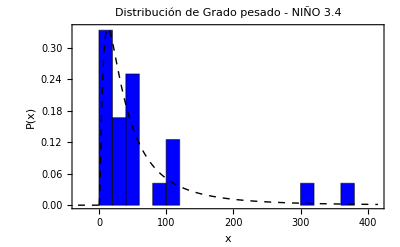

KolmogorovSmirnovTest::ties: Ties exist in the data and will be ignored for the KolmogorovSmirnov test, which assumes unique values.

Estadísticos descriptivos:

Media     = 14.5833

Varianza  = 36.3406

Asimetría = -0.1633

Curtosis  = 1.8833

Ajuste de distribuciones (candidatas):

Distribución | Ajuste | LogL | AIC
Power law | ParetoDistribution[3.,0.678595] | -95.0395 | 194.0789
Exponential | ExponentialDistribution[0.0685714] | -88.3171 | 178.6342
Lognormal | LogNormalDistribution[2.57225,0.506099] | -79.4439 | 162.8878
Gamma | GammaDistribution[4.80582,3.03451] | -77.7805 | 159.5609
Stretched exponential | WeibullDistribution[2.73951,16.4102] | -76.3836 | 156.7671

Distribución sugerida por FindDistribution:

Modelo = DiscreteUniformDistribution[{3, 18}]

LogL   = -Infinity

AIC    = Infinity

Mejor modelo (menor AIC entre candidatas): Stretched exponential, AIC = 156.7671

Detalles de la ley de potencia (Pareto):

α (exponente) = 0.6786

xmin (umbral) = 3.0000

p-valor KS    = 0.0026

→ Se rechaza la ley de potencia (p < 0.05).

IC 95% bootstrap para α = [0.6354, 1.6211]

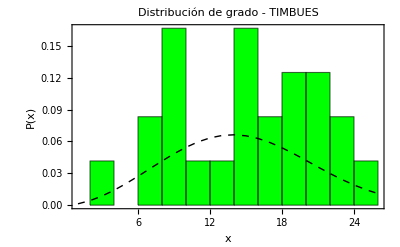

KolmogorovSmirnovTest::ties: Ties exist in the data and will be ignored for the KolmogorovSmirnov test, which assumes unique values.

Estadísticos descriptivos:

Media     = 69.0000

Varianza  = 5707.4783

Asimetría = 1.7073

Curtosis  = 5.3397

Ajuste de distribuciones (candidatas):

Distribución | Ajuste | LogL | AIC
Power law | ParetoDistribution[4.,0.439964] | -131.5264 | 267.0528
Exponential | ExponentialDistribution[0.0144928] | -125.6186 | 253.2371
Lognormal | LogNormalDistribution[3.65921,1.13393] | -124.8919 | 253.7839
Gamma | GammaDistribution[1.0036,68.7523] | -125.6185 | 255.2369
Stretched exponential | WeibullDistribution[0.970593,68.0317] | -125.5999 | 255.1999

Distribución sugerida por FindDistribution:

Modelo = No disponible

LogL   = N/A

AIC    = N/A

Mejor modelo (menor AIC entre candidatas): Exponential, AIC = 253.2371

Detalles de la ley de potencia (Pareto):

α (exponente) = 0.4400

xmin (umbral) = 4.0000

p-valor KS    = 0.0670

→ No se rechaza que los datos sigan una ley de potencia.

IC 95% bootstrap para α = [0.3799, 0.8124]

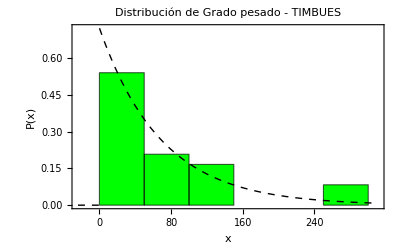

KolmogorovSmirnovTest::ties: Ties exist in the data and will be ignored for the KolmogorovSmirnov test, which assumes unique values.

Estadísticos descriptivos:

Media     = 10.9167

Varianza  = 43.3841

Asimetría = 0.4096

Curtosis  = 2.0580

Ajuste de distribuciones (candidatas):

Distribución | Ajuste | LogL | AIC
Power law | ParetoDistribution[2.,0.674487] | -85.6694 | 175.3388
Exponential | ExponentialDistribution[0.0916031] | -81.3670 | 164.7340
Lognormal | LogNormalDistribution[2.17575,0.701145] | -77.7517 | 159.5033
Gamma | GammaDistribution[2.48459,4.39375] | -76.9450 | 157.8899
Stretched exponential | WeibullDistribution[1.75681,12.2891] | -76.7327 | 157.4654

Distribución sugerida por FindDistribution:

Modelo = DiscreteUniformDistribution[{2, 16}]

LogL   = -Infinity

AIC    = Infinity

Mejor modelo (menor AIC entre candidatas): Stretched exponential, AIC = 157.4654

Detalles de la ley de potencia (Pareto):

α (exponente) = 0.6745

xmin (umbral) = 2.0000

p-valor KS    = 0.0385

→ Se rechaza la ley de potencia (p < 0.05).

IC 95% bootstrap para α = [0.6015, 1.0997]

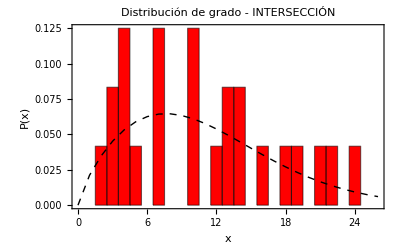

Estadísticos descriptivos:

Media     = 1597.0921

Varianza  =            6
1.2163 × 10

Asimetría = 0.3873

Curtosis  = 1.9587

Ajuste de distribuciones (candidatas):

Distribución | Ajuste | LogL | AIC
Power law | ParetoDistribution[200.,0.564076] | -207.4487 | 418.8974
Exponential | ExponentialDistribution[0.000626138] | -201.0226 | 404.0451
Lognormal | LogNormalDistribution[7.07113,0.851538] | -199.9046 | 403.8091
Gamma | GammaDistribution[1.78896,892.747] | -198.9763 | 401.9525
Stretched exponential | WeibullDistribution[1.46622,1764.86] | -198.7636 | 401.5272

Distribución sugerida por FindDistribution:

Modelo = UniformDistribution[{200., 3883.2}]

LogL   = -197.0769

AIC    = 396.1538

Mejor modelo (menor AIC entre candidatas): Stretched exponential, AIC = 401.5272

Detalles de la ley de potencia (Pareto):

α (exponente) = 0.5641

xmin (umbral) = 200.0000

p-valor KS    = 0.0908

→ No se rechaza que los datos sigan una ley de potencia.

IC 95% bootstrap para α = [0.4897, 0.9240]

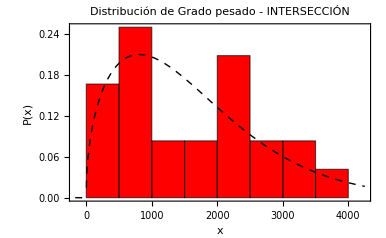

```mathematica
plotDistribution[NIÑOTIMBUES,"PlotLabel"->"Distribución de grado - NIÑO 3.4","PlotColor"->Blue,"Discrete"->True,"BootstrapReps"->500,"Bins"->200]

plotDistribution[NIÑOPESADOTIMBUES,"PlotLabel"->"Distribución de Grado pesado - NIÑO 3.4","PlotColor"->Blue,"Discrete"->False,"BootstrapReps"->500,"Bins"->20]

plotDistribution[TIMBUES,"PlotLabel"->"Distribución de grado - TIMBUES","PlotColor"->Green,"Discrete"->True,"BootstrapReps"->500,"Bins"->10]

plotDistribution[TIMBUESPESADO,"PlotLabel"->"Distribución de Grado pesado - TIMBUES","PlotColor"->Green,"Discrete"->False,"BootstrapReps"->500,"Bins"->7]

plotDistribution[INTERTIMBUES,"PlotLabel"->"Distribución de grado - INTERSECCIÓN","PlotColor"->Red,"Discrete"->True,"BootstrapReps"->500,"Bins"->50]

plotDistribution[INTERTIMBUESPESADO,"PlotLabel"->"Distribución de Grado pesado - INTERSECCIÓN","PlotColor"->Red,"Discrete"->False,"BootstrapReps"->500,"Bins"->8]
```

# MANAOS

```mathematica
NIÑOMANAOS = {22, 18, 10, 12, 1, 14, 15, 7, 9, 10, 4, 10, 10, 6, 12, 9, 4, 17, 10, 4, 13, 12, 20, 25};

NIÑOPESADOMANAOS = {220, 66, 24, 28, 2, 26, 61, 8, 12, 24, 4, 34, 38, 8, 23, 12, 6, 74,
       20, 4, 30, 32, 82, 280};

MANAOS = {23, 18, 14, 16, 6, 16, 20, 14, 6, 13, 5, 12, 11, 2, 13, 7, 10, 22,
       16, 7, 17, 13, 19, 24};

MANAOSPESADO = {169, 66, 34, 46, 10, 34, 72, 30, 8, 24, 8, 32, 34, 2, 34, 10, 24,
       76, 30, 12, 39, 36, 70, 218};

INTERMANAOS = {20, 14, 7, 10, 1, 11, 14, 5, 4, 7, 2, 7, 7, 1, 9, 4, 3, 15, 8, 2,
       11, 9, 17, 24};

INTERMANAOSPESADO = {2768.92443578, 1778.0952381, 923.80952381, 1815., 250.,
       1636.66666667, 1832.12121212, 1300., 400., 670.,
       400., 576.66666667, 456.28205128, 100., 1260.,
       400., 550., 2035., 1100., 200.,
       1514.28571429, 1068.33333333, 2263.94927536, 2907.8369228};
```

KolmogorovSmirnovTest::ties: Ties exist in the data and will be ignored for the KolmogorovSmirnov test, which assumes unique values.

Estadísticos descriptivos:

Media     = 11.4167

Varianza  = 35.2971

Asimetría = 0.4679

Curtosis  = 2.8135

Ajuste de distribuciones (candidatas):

Distribución | Ajuste | LogL | AIC
Power law | ParetoDistribution[1.,0.442805] | -97.7510 | 199.5019
Exponential | ExponentialDistribution[0.0875912] | -82.4418 | 166.8836
Lognormal | LogNormalDistribution[2.25833,0.683098] | -79.1077 | 162.2153
Gamma | GammaDistribution[2.98521,3.8244] | -76.4608 | 156.9215
Stretched exponential | WeibullDistribution[2.02536,12.8449] | -75.5827 | 155.1654

Distribución sugerida por FindDistribution:

Modelo = NegativeBinomialDistribution[4, 0.362369]

LogL   = -84.9484

AIC    = 173.8969

Mejor modelo (menor AIC entre candidatas): Stretched exponential, AIC = 155.1654

Detalles de la ley de potencia (Pareto):

α (exponente) = 0.4428

xmin (umbral) = 1.0000

p-valor KS    = 0.0003

→ Se rechaza la ley de potencia (p < 0.05).

IC 95% bootstrap para α = [0.4137, 1.2382]

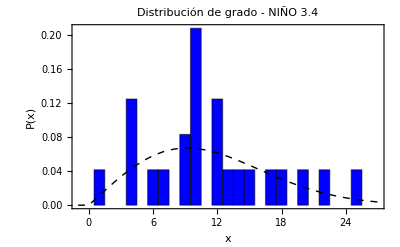

KolmogorovSmirnovTest::ties: Ties exist in the data and will be ignored for the KolmogorovSmirnov test, which assumes unique values.

Estadísticos descriptivos:

Media     = 46.5833

Varianza  = 4502.1667

Asimetría = 2.5611

Curtosis  = 8.7236

Ajuste de distribuciones (candidatas):

Distribución | Ajuste | LogL | AIC
Power law | ParetoDistribution[2.,0.407478] | -121.0809 | 246.1618
Exponential | ExponentialDistribution[0.0214669] | -116.1898 | 234.3797
Lognormal | LogNormalDistribution[3.14727,1.1905] | -113.7739 | 231.5479
Gamma | GammaDistribution[0.848672,54.8897] | -115.9652 | 235.9303
Stretched exponential | WeibullDistribution[0.854289,42.3078] | -115.5688 | 235.1375

Distribución sugerida por FindDistribution:

Modelo = No disponible

LogL   = N/A

AIC    = N/A

Mejor modelo (menor AIC entre candidatas): Lognormal, AIC = 231.5479

Detalles de la ley de potencia (Pareto):

α (exponente) = 0.4075

xmin (umbral) = 2.0000

p-valor KS    = 0.0423

→ Se rechaza la ley de potencia (p < 0.05).

IC 95% bootstrap para α = [0.3655, 0.6835]

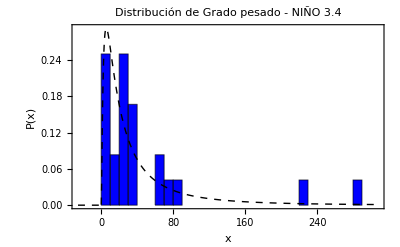

KolmogorovSmirnovTest::ties: Ties exist in the data and will be ignored for the KolmogorovSmirnov test, which assumes unique values.

Estadísticos descriptivos:

Media     = 13.5000

Varianza  = 35.6522

Asimetría = -0.0707

Curtosis  = 2.2023

Ajuste de distribuciones (candidatas):

Distribución | Ajuste | LogL | AIC
Power law | ParetoDistribution[2.,0.562234] | -97.1425 | 198.2850
Exponential | ExponentialDistribution[0.0740741] | -86.4646 | 174.9291
Lognormal | LogNormalDistribution[2.47177,0.57371] | -80.0418 | 164.0835
Gamma | GammaDistribution[3.97804,3.39363] | -77.8088 | 159.6176
Stretched exponential | WeibullDistribution[2.48771,15.1941] | -76.3246 | 156.6491

Distribución sugerida por FindDistribution:

Modelo = DiscreteUniformDistribution[{2, 18}]

LogL   = -Infinity

AIC    = Infinity

Mejor modelo (menor AIC entre candidatas): Stretched exponential, AIC = 156.6491

Detalles de la ley de potencia (Pareto):

α (exponente) = 0.5622

xmin (umbral) = 2.0000

p-valor KS    = 0.0014

→ Se rechaza la ley de potencia (p < 0.05).

IC 95% bootstrap para α = [0.5183, 1.3765]

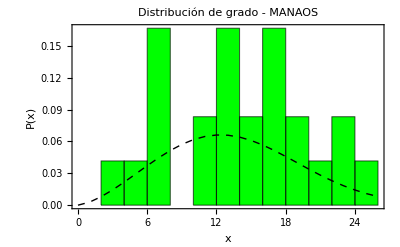

KolmogorovSmirnovTest::ties: Ties exist in the data and will be ignored for the KolmogorovSmirnov test, which assumes unique values.

Estadísticos descriptivos:

Media     = 46.5833

Varianza  = 2531.7319

Asimetría = 2.2822

Curtosis  = 7.8130

Ajuste de distribuciones (candidatas):

Distribución | Ajuste | LogL | AIC
Power law | ParetoDistribution[2.,0.371104] | -129.0980 | 262.1960
Exponential | ExponentialDistribution[0.0214669] | -116.1898 | 234.3797
Lognormal | LogNormalDistribution[3.38781,1.00871] | -115.5701 | 235.1403
Gamma | GammaDistribution[1.24291,37.4793] | -115.8573 | 235.7147
Stretched exponential | WeibullDistribution[1.07883,48.119] | -116.0664 | 236.1328

Distribución sugerida por FindDistribution:

Modelo = No disponible

LogL   = N/A

AIC    = N/A

Mejor modelo (menor AIC entre candidatas): Exponential, AIC = 234.3797

Detalles de la ley de potencia (Pareto):

α (exponente) = 0.3711

xmin (umbral) = 2.0000

p-valor KS    = 0.0027

→ Se rechaza la ley de potencia (p < 0.05).

IC 95% bootstrap para α = [0.3362, 0.8978]

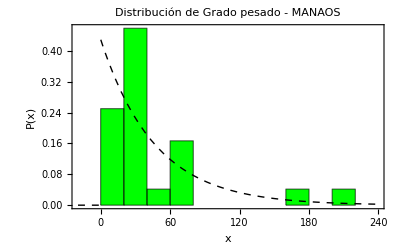

KolmogorovSmirnovTest::ties: Ties exist in the data and will be ignored for the KolmogorovSmirnov test, which assumes unique values.

Estadísticos descriptivos:

Media     = 8.8333

Varianza  = 36.9275

Asimetría = 0.7625

Curtosis  = 3.0019

Ajuste de distribuciones (candidatas):

Distribución | Ajuste | LogL | AIC
Power law | ParetoDistribution[1.,0.530786] | -84.4175 | 172.8351
Exponential | ExponentialDistribution[0.113208] | -76.2848 | 154.5696
Lognormal | LogNormalDistribution[1.884,0.858942] | -75.6212 | 155.2425
Gamma | GammaDistribution[1.84681,4.78302] | -74.0368 | 152.0736
Stretched exponential | WeibullDistribution[1.48858,9.77052] | -73.7932 | 151.5864

Distribución sugerida por FindDistribution:

Modelo = DiscreteUniformDistribution[{1, 15}]

LogL   = -Infinity

AIC    = Infinity

Mejor modelo (menor AIC entre candidatas): Stretched exponential, AIC = 151.5864

Detalles de la ley de potencia (Pareto):

α (exponente) = 0.5308

xmin (umbral) = 1.0000

p-valor KS    = 0.0140

→ Se rechaza la ley de potencia (p < 0.05).

IC 95% bootstrap para α = [0.4647, 0.8829]

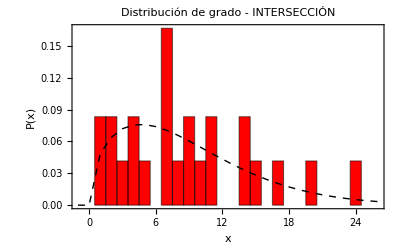

KolmogorovSmirnovTest::ties: Ties exist in the data and will be ignored for the KolmogorovSmirnov test, which assumes unique values.

Estadísticos descriptivos:

Media     = 1175.2905

Varianza  = 669087.7465

Asimetría = 0.5469

Curtosis  = 2.2936

Ajuste de distribuciones (candidatas):

Distribución | Ajuste | LogL | AIC
Power law | ParetoDistribution[100.,0.463721] | -204.7226 | 413.4452
Exponential | ExponentialDistribution[0.000850853] | -193.6625 | 389.3250
Lognormal | LogNormalDistribution[6.76164,0.871206] | -193.0248 | 390.0496
Gamma | GammaDistribution[1.77375,662.602] | -191.6691 | 387.3382
Stretched exponential | WeibullDistribution[1.45728,1296.84] | -191.4430 | 386.8860

Distribución sugerida por FindDistribution:

Modelo = UniformDistribution[{100.077, 2907.89}]

LogL   = -Infinity

AIC    = Infinity

Mejor modelo (menor AIC entre candidatas): Stretched exponential, AIC = 386.8860

Detalles de la ley de potencia (Pareto):

α (exponente) = 0.4637

xmin (umbral) = 100.0000

p-valor KS    = 0.0040

→ Se rechaza la ley de potencia (p < 0.05).

IC 95% bootstrap para α = [0.4183, 0.8836]

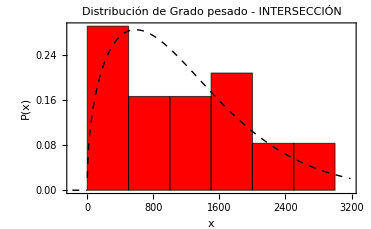

```mathematica
plotDistribution[NIÑOMANAOS,"PlotLabel"->"Distribución de grado - NIÑO 3.4","PlotColor"->Blue,"Discrete"->True,"BootstrapReps"->500,"Bins"->200]

plotDistribution[NIÑOPESADOMANAOS,"PlotLabel"->"Distribución de Grado pesado - NIÑO 3.4","PlotColor"->Blue,"Discrete"->False,"BootstrapReps"->500,"Bins"->20]

plotDistribution[MANAOS,"PlotLabel"->"Distribución de grado - MANAOS","PlotColor"->Green,"Discrete"->True,"BootstrapReps"->500,"Bins"->10]

plotDistribution[MANAOSPESADO,"PlotLabel"->"Distribución de Grado pesado - MANAOS","PlotColor"->Green,"Discrete"->False,"BootstrapReps"->500,"Bins"->10]

plotDistribution[INTERMANAOS,"PlotLabel"->"Distribución de grado - INTERSECCIÓN","PlotColor"->Red,"Discrete"->True,"BootstrapReps"->500,"Bins"->50]

plotDistribution[INTERMANAOSPESADO,"PlotLabel"->"Distribución de Grado pesado - INTERSECCIÓN","PlotColor"->Red,"Discrete"->False,"BootstrapReps"->500,"Bins"->8]
```

# OBIDOS

```mathematica
NIÑOOBIDOS = {22, 20, 10, 13, 2, 15, 17, 7, 9, 10, 6, 10, 10, 6, 13, 9, 4, 17, 11, 4, 13, 13, 20, 25};

NIÑOOBIDOSPESADO = {239, 74, 28, 34, 4, 28, 70, 10, 12, 25, 6, 36, 40, 8, 28, 12, 6, 82,
       24, 4, 32, 35, 86, 309};

OBIDOS = {22, 17, 12, 14, 6, 11, 21, 8, 8, 15, 3, 20, 15, 2, 11, 4, 6, 21, 12, 7, 16, 15, 19, 23};

OBIDOSPESADO = {218, 79, 22, 55, 6, 21, 88, 12, 8, 31, 5, 56, 49, 2, 34, 8, 6, 96,
       27, 12, 46, 20, 91, 240};

INTEROBIDOS = {21, 15, 8, 10, 1, 8, 15, 4, 3, 8, 2, 9, 9, 0, 8, 2, 1, 15, 6, 2, 9, 9, 18, 23};

INTEROBIDOSPESADO = {2783.11091686, 1897.0432019, 604.76190476, 1561.66666667, 33.33333333,
       960., 1921.42857143, 583.33333333, 200., 830.,
       400., 892.22222222, 1010.23809524, 0., 1170.,
       300., 50., 2372.35507246, 828.57142857, 300.,
       1050., 470., 3037.91666667, 2028.72061868};
```

KolmogorovSmirnovTest::ties: Ties exist in the data and will be ignored for the KolmogorovSmirnov test, which assumes unique values.

Estadísticos descriptivos:

Media     = 11.4167

Varianza  = 35.2971

Asimetría = 0.4679

Curtosis  = 2.8135

Ajuste de distribuciones (candidatas):

Distribución | Ajuste | LogL | AIC
Power law | ParetoDistribution[1.,0.442805] | -97.7510 | 199.5019
Exponential | ExponentialDistribution[0.0875912] | -82.4418 | 166.8836
Lognormal | LogNormalDistribution[2.25833,0.683098] | -79.1077 | 162.2153
Gamma | GammaDistribution[2.98521,3.8244] | -76.4608 | 156.9215
Stretched exponential | WeibullDistribution[2.02536,12.8449] | -75.5827 | 155.1654

Distribución sugerida por FindDistribution:

Modelo = NegativeBinomialDistribution[4, 0.362369]

LogL   = -84.9484

AIC    = 173.8969

Mejor modelo (menor AIC entre candidatas): Stretched exponential, AIC = 155.1654

Detalles de la ley de potencia (Pareto):

α (exponente) = 0.4428

xmin (umbral) = 1.0000

p-valor KS    = 0.0003

→ Se rechaza la ley de potencia (p < 0.05).

IC 95% bootstrap para α = [0.4171, 1.2685]

-Graphics-

KolmogorovSmirnovTest::ties: Ties exist in the data and will be ignored for the KolmogorovSmirnov test, which assumes unique values.

Estadísticos descriptivos:

Media     = 46.5833

Varianza  = 4502.1667

Asimetría = 2.5611

Curtosis  = 8.7236

Ajuste de distribuciones (candidatas):

Distribución | Ajuste | LogL | AIC
Power law | ParetoDistribution[2.,0.407478] | -121.0809 | 246.1618
Exponential | ExponentialDistribution[0.0214669] | -116.1898 | 234.3797
Lognormal | LogNormalDistribution[3.14727,1.1905] | -113.7739 | 231.5479
Gamma | GammaDistribution[0.848672,54.8897] | -115.9652 | 235.9303
Stretched exponential | WeibullDistribution[0.854289,42.3078] | -115.5688 | 235.1375

Distribución sugerida por FindDistribution:

Modelo = No disponible

LogL   = N/A

AIC    = N/A

Mejor modelo (menor AIC entre candidatas): Lognormal, AIC = 231.5479

Detalles de la ley de potencia (Pareto):

α (exponente) = 0.4075

xmin (umbral) = 2.0000

p-valor KS    = 0.0423

→ Se rechaza la ley de potencia (p < 0.05).

IC 95% bootstrap para α = [0.3641, 0.6995]

-Graphics-

KolmogorovSmirnovTest::ties: Ties exist in the data and will be ignored for the KolmogorovSmirnov test, which assumes unique values.

Estadísticos descriptivos:

Media     = 13.5000

Varianza  = 35.6522

Asimetría = -0.0707

Curtosis  = 2.2023

Ajuste de distribuciones (candidatas):

Distribución | Ajuste | LogL | AIC
Power law | ParetoDistribution[2.,0.562234] | -97.1425 | 198.2850
Exponential | ExponentialDistribution[0.0740741] | -86.4646 | 174.9291
Lognormal | LogNormalDistribution[2.47177,0.57371] | -80.0418 | 164.0835
Gamma | GammaDistribution[3.97804,3.39363] | -77.8088 | 159.6176
Stretched exponential | WeibullDistribution[2.48771,15.1941] | -76.3246 | 156.6491

Distribución sugerida por FindDistribution:

Modelo = DiscreteUniformDistribution[{2, 18}]

LogL   = -Infinity

AIC    = Infinity

Mejor modelo (menor AIC entre candidatas): Stretched exponential, AIC = 156.6491

Detalles de la ley de potencia (Pareto):

α (exponente) = 0.5622

xmin (umbral) = 2.0000

p-valor KS    = 0.0014

→ Se rechaza la ley de potencia (p < 0.05).

IC 95% bootstrap para α = [0.5232, 1.4289]

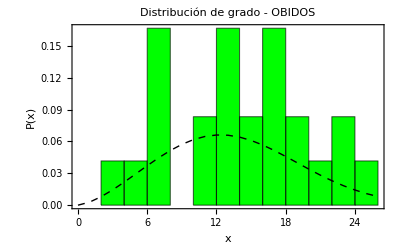

KolmogorovSmirnovTest::ties: Ties exist in the data and will be ignored for the KolmogorovSmirnov test, which assumes unique values.

Estadísticos descriptivos:

Media     = 46.5833

Varianza  = 2531.7319

Asimetría = 2.2822

Curtosis  = 7.8130

Ajuste de distribuciones (candidatas):

Distribución | Ajuste | LogL | AIC
Power law | ParetoDistribution[2.,0.371104] | -129.0980 | 262.1960
Exponential | ExponentialDistribution[0.0214669] | -116.1898 | 234.3797
Lognormal | LogNormalDistribution[3.38781,1.00871] | -115.5701 | 235.1403
Gamma | GammaDistribution[1.24291,37.4793] | -115.8573 | 235.7147
Stretched exponential | WeibullDistribution[1.07883,48.119] | -116.0664 | 236.1328

Distribución sugerida por FindDistribution:

Modelo = No disponible

LogL   = N/A

AIC    = N/A

Mejor modelo (menor AIC entre candidatas): Exponential, AIC = 234.3797

Detalles de la ley de potencia (Pareto):

α (exponente) = 0.3711

xmin (umbral) = 2.0000

p-valor KS    = 0.0027

→ Se rechaza la ley de potencia (p < 0.05).

IC 95% bootstrap para α = [0.3329, 0.8740]

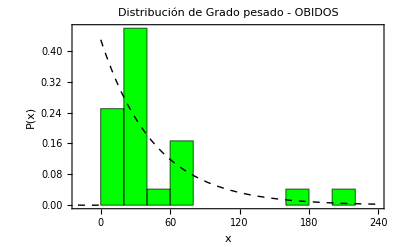

KolmogorovSmirnovTest::ties: Ties exist in the data and will be ignored for the KolmogorovSmirnov test, which assumes unique values.

Estadísticos descriptivos:

Media     = 8.8333

Varianza  = 36.9275

Asimetría = 0.7625

Curtosis  = 3.0019

Ajuste de distribuciones (candidatas):

Distribución | Ajuste | LogL | AIC
Power law | ParetoDistribution[1.,0.530786] | -84.4175 | 172.8351
Exponential | ExponentialDistribution[0.113208] | -76.2848 | 154.5696
Lognormal | LogNormalDistribution[1.884,0.858942] | -75.6212 | 155.2425
Gamma | GammaDistribution[1.84681,4.78302] | -74.0368 | 152.0736
Stretched exponential | WeibullDistribution[1.48858,9.77052] | -73.7932 | 151.5864

Distribución sugerida por FindDistribution:

Modelo = DiscreteUniformDistribution[{1, 15}]

LogL   = -Infinity

AIC    = Infinity

Mejor modelo (menor AIC entre candidatas): Stretched exponential, AIC = 151.5864

Detalles de la ley de potencia (Pareto):

α (exponente) = 0.5308

xmin (umbral) = 1.0000

p-valor KS    = 0.0140

→ Se rechaza la ley de potencia (p < 0.05).

IC 95% bootstrap para α = [0.4612, 0.8341]

-Graphics-

KolmogorovSmirnovTest::ties: Ties exist in the data and will be ignored for the KolmogorovSmirnov test, which assumes unique values.

Estadísticos descriptivos:

Media     = 1175.2905

Varianza  = 669087.7465

Asimetría = 0.5469

Curtosis  = 2.2936

Ajuste de distribuciones (candidatas):

Distribución | Ajuste | LogL | AIC
Power law | ParetoDistribution[100.,0.463721] | -204.7226 | 413.4452
Exponential | ExponentialDistribution[0.000850853] | -193.6625 | 389.3250
Lognormal | LogNormalDistribution[6.76164,0.871206] | -193.0248 | 390.0496
Gamma | GammaDistribution[1.77375,662.602] | -191.6691 | 387.3382
Stretched exponential | WeibullDistribution[1.45728,1296.84] | -191.4430 | 386.8860

Distribución sugerida por FindDistribution:

Modelo = UniformDistribution[{100.077, 2907.89}]

LogL   = -Infinity

AIC    = Infinity

Mejor modelo (menor AIC entre candidatas): Stretched exponential, AIC = 386.8860

Detalles de la ley de potencia (Pareto):

α (exponente) = 0.4637

xmin (umbral) = 100.0000

p-valor KS    = 0.0040

→ Se rechaza la ley de potencia (p < 0.05).

IC 95% bootstrap para α = [0.4216, 0.9415]

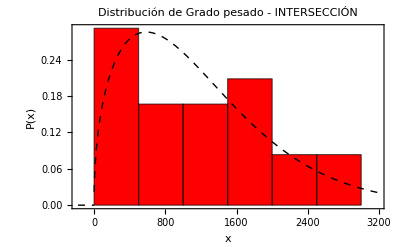

```mathematica
plotDistribution[NIÑOMANAOS,"PlotLabel"->"Distribución de grado - NIÑO 3.4","PlotColor"->Blue,"Discrete"->True,"BootstrapReps"->500,"Bins"->200]

plotDistribution[NIÑOPESADOMANAOS,"PlotLabel"->"Distribución de Grado pesado - NIÑO 3.4","PlotColor"->Blue,"Discrete"->False,"BootstrapReps"->500,"Bins"->20]

plotDistribution[MANAOS,"PlotLabel"->"Distribución de grado - OBIDOS","PlotColor"->Green,"Discrete"->True,"BootstrapReps"->500,"Bins"->10]

plotDistribution[MANAOSPESADO,"PlotLabel"->"Distribución de Grado pesado - OBIDOS","PlotColor"->Green,"Discrete"->False,"BootstrapReps"->500,"Bins"->10]

plotDistribution[INTERMANAOS,"PlotLabel"->"Distribución de grado - INTERSECCIÓN","PlotColor"->Red,"Discrete"->True,"BootstrapReps"->500,"Bins"->50]

plotDistribution[INTERMANAOSPESADO,"PlotLabel"->"Distribución de Grado pesado - INTERSECCIÓN","PlotColor"->Red,"Discrete"->False,"BootstrapReps"->500,"Bins"->8]
```

# TABATINGA

```mathematica
NIÑOTABATINGA = {21, 15, 8, 11, 1, 11, 11, 7, 5, 10, 2, 9, 10, 4, 10, 6, 4, 16, 8, 4, 11, 9, 18, 25};

NIÑOTABATINGAPESADO = {186, 50, 20, 22, 2, 18, 43, 8, 6, 16, 2, 26, 32, 4, 15, 8, 6, 53,
       14, 4, 22, 21, 61, 237};

TABATINGA = {25, 21, 18, 13, 10, 17, 19, 21, 10, 14, 11, 19, 18, 10, 20, 12, 13, 21,
       13, 13, 16, 19, 22, 23};

TABATINGAPESADO = {80, 61, 36, 26, 12, 37, 47, 40, 18, 20, 16, 47, 40, 12, 36, 20, 24,
       44, 20, 19, 29, 36, 62, 94};

INTERTABATINGA = {21, 14, 7, 10, 1, 8, 8, 6, 2, 7, 1, 9, 10, 3, 9, 5, 2, 15, 6, 3, 8, 8, 16, 23};

INTERTABATINGAPESADO = {1814.09420367, 2237.87878788, 878.57142857, 1250., 100.,
       1691.66666667, 767.85714286, 1150., 200., 600.,
       200., 1516.66666667, 1883.33333333, 300., 1550.,
       800., 150., 1330.71428571, 816.66666667, 400.,
       1123.33333333, 1225., 2449.44444444, 1940.77944653};
```

KolmogorovSmirnovTest::ties: Ties exist in the data and will be ignored for the KolmogorovSmirnov test, which assumes unique values.

Estadísticos descriptivos:

Media     = 9.8333

Varianza  = 34.2319

Asimetría = 0.8501

Curtosis  = 3.4555

Ajuste de distribuciones (candidatas):

Distribución | Ajuste | LogL | AIC
Power law | ParetoDistribution[1.,0.481095] | -91.4468 | 186.8936
Exponential | ExponentialDistribution[0.101695] | -78.8587 | 159.7173
Lognormal | LogNormalDistribution[2.07859,0.717473] | -75.9722 | 155.9445
Gamma | GammaDistribution[2.56771,3.82961] | -74.1675 | 152.3350
Stretched exponential | WeibullDistribution[1.77521,11.0487] | -73.9044 | 151.8089

Distribución sugerida por FindDistribution:

Modelo = DiscreteUniformDistribution[{1, 15}]

LogL   = -Infinity

AIC    = Infinity

Mejor modelo (menor AIC entre candidatas): Stretched exponential, AIC = 151.8089

Detalles de la ley de potencia (Pareto):

α (exponente) = 0.4811

xmin (umbral) = 1.0000

p-valor KS    = 0.0005

→ Se rechaza la ley de potencia (p < 0.05).

IC 95% bootstrap para α = [0.4468, 1.2840]

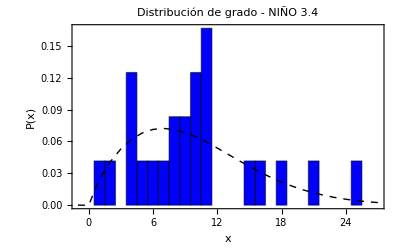

KolmogorovSmirnovTest::ties: Ties exist in the data and will be ignored for the KolmogorovSmirnov test, which assumes unique values.

Estadísticos descriptivos:

Media     = 36.5000

Varianza  = 3235.6522

Asimetría = 2.6828

Curtosis  = 9.2093

Ajuste de distribuciones (candidatas):

Distribución | Ajuste | LogL | AIC
Power law | ParetoDistribution[2.,0.464484] | -110.7096 | 225.4191
Exponential | ExponentialDistribution[0.0273973] | -110.3355 | 222.6710
Lognormal | LogNormalDistribution[2.84607,1.20952] | -106.9256 | 217.8512
Gamma | GammaDistribution[0.791174,46.134] | -109.8623 | 223.7247
Stretched exponential | WeibullDistribution[0.81569,31.8658] | -109.2436 | 222.4872

Distribución sugerida por FindDistribution:

Modelo = No disponible

LogL   = N/A

AIC    = N/A

Mejor modelo (menor AIC entre candidatas): Lognormal, AIC = 217.8512

Detalles de la ley de potencia (Pareto):

α (exponente) = 0.4645

xmin (umbral) = 2.0000

p-valor KS    = 0.0614

→ No se rechaza que los datos sigan una ley de potencia.

IC 95% bootstrap para α = [0.3983, 0.7077]

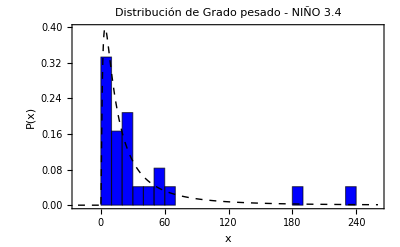

KolmogorovSmirnovTest::ties: Ties exist in the data and will be ignored for the KolmogorovSmirnov test, which assumes unique values.

Estadísticos descriptivos:

Media     = 16.5833

Varianza  = 20.6014

Asimetría = 0.0181

Curtosis  = 1.7868

Ajuste de distribuciones (candidatas):

Distribución | Ajuste | LogL | AIC
Power law | ParetoDistribution[10.,2.13867] | -72.2396 | 148.4792
Exponential | ExponentialDistribution[0.0603015] | -91.4016 | 184.8031
Lognormal | LogNormalDistribution[2.77017,0.281362] | -70.1038 | 144.2076
Gamma | GammaDistribution[13.2425,1.25228] | -69.8393 | 143.6785
Stretched exponential | WeibullDistribution[4.25181,18.2799] | -69.5886 | 143.1772

Distribución sugerida por FindDistribution:

Modelo = DiscreteUniformDistribution[{10, 23}]

LogL   = -Infinity

AIC    = Infinity

Mejor modelo (menor AIC entre candidatas): Stretched exponential, AIC = 143.1772

Detalles de la ley de potencia (Pareto):

α (exponente) = 2.1387

xmin (umbral) = 10.0000

p-valor KS    = 0.1642

→ No se rechaza que los datos sigan una ley de potencia.

IC 95% bootstrap para α = [1.7238, 2.9756]

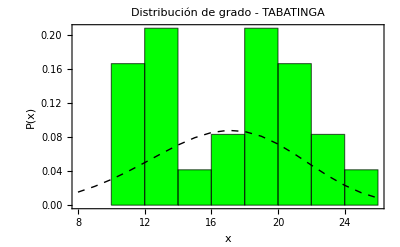

KolmogorovSmirnovTest::ties: Ties exist in the data and will be ignored for the KolmogorovSmirnov test, which assumes unique values.

Estadísticos descriptivos:

Media     = 36.5000

Varianza  = 441.7391

Asimetría = 1.1472

Curtosis  = 3.8811

Ajuste de distribuciones (candidatas):

Distribución | Ajuste | LogL | AIC
Power law | ParetoDistribution[12.,1.03819] | -105.8554 | 215.7108
Exponential | ExponentialDistribution[0.0273973] | -110.3355 | 222.6710
Lognormal | LogNormalDistribution[3.44812,0.548169] | -102.3813 | 208.7626
Gamma | GammaDistribution[3.50932,10.4009] | -102.8782 | 209.7564
Stretched exponential | WeibullDistribution[1.90662,41.3945] | -103.8518 | 211.7036

Distribución sugerida por FindDistribution:

Modelo = No disponible

LogL   = N/A

AIC    = N/A

Mejor modelo (menor AIC entre candidatas): Lognormal, AIC = 208.7626

Detalles de la ley de potencia (Pareto):

α (exponente) = 1.0382

xmin (umbral) = 12.0000

p-valor KS    = 0.1609

→ No se rechaza que los datos sigan una ley de potencia.

IC 95% bootstrap para α = [0.8673, 1.6271]

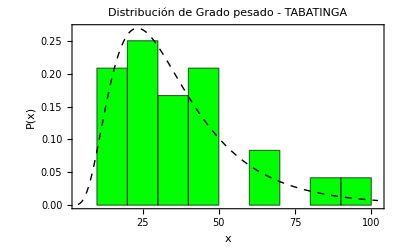

KolmogorovSmirnovTest::ties: Ties exist in the data and will be ignored for the KolmogorovSmirnov test, which assumes unique values.

Estadísticos descriptivos:

Media     = 8.4167

Varianza  = 34.2536

Asimetría = 0.9441

Curtosis  = 3.3968

Ajuste de distribuciones (candidatas):

Distribución | Ajuste | LogL | AIC
Power law | ParetoDistribution[1.,0.541939] | -82.9878 | 169.9756
Exponential | ExponentialDistribution[0.118812] | -75.1251 | 152.2503
Lognormal | LogNormalDistribution[1.84522,0.838751] | -74.1197 | 152.2394
Gamma | GammaDistribution[1.90422,4.42001] | -72.6767 | 149.3534
Stretched exponential | WeibullDistribution[1.49357,9.32296] | -72.5387 | 149.0775

Distribución sugerida por FindDistribution:

Modelo = DiscreteUniformDistribution[{1, 14}]

LogL   = -Infinity

AIC    = Infinity

Mejor modelo (menor AIC entre candidatas): Stretched exponential, AIC = 149.0775

Detalles de la ley de potencia (Pareto):

α (exponente) = 0.5419

xmin (umbral) = 1.0000

p-valor KS    = 0.0074

→ Se rechaza la ley de potencia (p < 0.05).

IC 95% bootstrap para α = [0.4696, 0.8417]

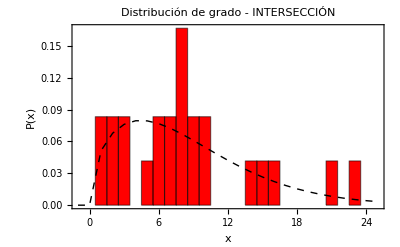

KolmogorovSmirnovTest::ties: Ties exist in the data and will be ignored for the KolmogorovSmirnov test, which assumes unique values.

Estadísticos descriptivos:

Media     = 1099.0003

Varianza  = 478213.1534

Asimetría = 0.1878

Curtosis  = 2.0235

Ajuste de distribuciones (candidatas):

Distribución | Ajuste | LogL | AIC
Power law | ParetoDistribution[100.,0.47681] | -202.6339 | 409.2679
Exponential | ExponentialDistribution[0.000909918] | -192.0517 | 386.1035
Lognormal | LogNormalDistribution[6.70244,0.896556] | -192.2925 | 388.5850
Gamma | GammaDistribution[1.81716,604.789] | -189.9072 | 383.8144
Stretched exponential | WeibullDistribution[1.56439,1216.5] | -189.1852 | 382.3704

Distribución sugerida por FindDistribution:

Modelo = UniformDistribution[{99.9023, 2449.48}]

LogL   = -186.2878

AIC    = 374.5756

Mejor modelo (menor AIC entre candidatas): Stretched exponential, AIC = 382.3704

Detalles de la ley de potencia (Pareto):

α (exponente) = 0.4768

xmin (umbral) = 100.0000

p-valor KS    = 0.0079

→ Se rechaza la ley de potencia (p < 0.05).

IC 95% bootstrap para α = [0.4323, 0.7235]

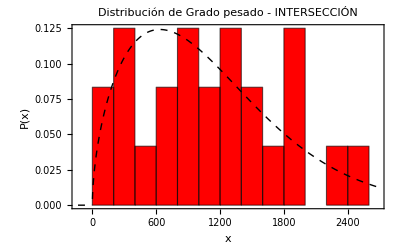

```mathematica
plotDistribution[NIÑOTABATINGA,"PlotLabel"->"Distribución de grado - NIÑO 3.4","PlotColor"->Blue,"Discrete"->True,"BootstrapReps"->500,"Bins"->200]

plotDistribution[NIÑOTABATINGAPESADO,"PlotLabel"->"Distribución de Grado pesado - NIÑO 3.4","PlotColor"->Blue,"Discrete"->False,"BootstrapReps"->500,"Bins"->20]

plotDistribution[TABATINGA,"PlotLabel"->"Distribución de grado - TABATINGA","PlotColor"->Green,"Discrete"->True,"BootstrapReps"->500,"Bins"->10]

plotDistribution[TABATINGAPESADO,"PlotLabel"->"Distribución de Grado pesado - TABATINGA","PlotColor"->Green,"Discrete"->False,"BootstrapReps"->500,"Bins"->10]

plotDistribution[INTERTABATINGA,"PlotLabel"->"Distribución de grado - INTERSECCIÓN","PlotColor"->Red,"Discrete"->True,"BootstrapReps"->500,"Bins"->50]

plotDistribution[INTERTABATINGAPESADO,"PlotLabel"->"Distribución de Grado pesado - INTERSECCIÓN","PlotColor"->Red,"Discrete"->False,"BootstrapReps"->500,"Bins"->8]
```